# Blatt 4 - Optimierung der Emittanz im FODO-Lattice

Jonas Neundorf & Jan Skottke

Definiere Konstanten

```mathematica
constants={c-> 3.*10^8, q-> 1.602*10^-19,m-> 0.511*10^-3,r0-> 2.818*10^-15,cq-> 3.8*10^-13};
```

Definiere Twiss-Parameter

```mathematica
β:=(2*(s^2+L*s*(-1+2*κ)+L^2*κ*(-1+2*κ)))/(L*√(-1+4*κ^2))
```

```mathematica
α:=-1/2*D[β,s]
```

```mathematica
γ:=(1+α^2)/β
```

Übernehme Funktionen von Blatt 3. Die Formeln sind der Musterlösung entnommen.

```mathematica
η[s_]:=1/(L*θ)(L*Cos[(s*θ)/L] (s+L*(-1+κ)+(s+L*κ)*Cos[θ]+θ*κ*(s+2*L*κ)*Sin[θ])+L*(L-2*s-L*κ-L*κ*Cos[θ]+θ*κ*(-L+s+2*L*κ)*Sin[θ])+(θ*(s^2+L*s*(-1+2*κ)+L^2*κ*(-1+2*κ))-L*θ*κ*(s+2*L*κ)*Cos[θ]+L*(s+L*κ)*Sin[θ])*Sin[(s*θ)/L])
```

```mathematica
dd :=Series[1/ρ*Integrate[η[s],{s,0,L}]/L //. L->ρ*θ,{θ,0,2}]//Normal
```

```mathematica
ηser=Series[η[s],{θ,0,2}]//Normal//FullSimplify
```

1/2 θ (s^2/L+s (-1+4 κ)+2 L κ (-1+4 κ))

```mathematica
h[s_]:=γ*(ηser)^2+2*α*ηser*D[ηser,s]+β*(D[ηser,s])^2
```

```mathematica
hmitser=Integrate[h[s],{s,0,L}]/L;
```

#### Berechne die Gleichgewichtsemittanz

```mathematica
ϵ0=Simplify[cq*((hmitser*γrel^2)/((1-dd)*ρ))//.L-> ρ*θ,Assumptions->κ>1/2]
```

-(cq γrel^2 θ^3 (1-180 κ^2+960 κ^4))/(5 √(-1+4 κ^2) (-12+θ^2 (-1+48 κ^2)))

Der gesamte Term geht mit θ^3 in der Näherung kleiner Winkel, da θ in der Größenordnung von 10^-2 ist, und θ^2<< 12. Somit würde ein θ->0 die Emittanz minimieren.

Für Kreisbeschleuniger gibt es die Begrenzung des Umfanges (Geld, Platz).
Der gesamte Term geht mit θ^3 in der Näherung kleiner Winkel, da θ in der Größenordnung von 10^-2 ist. Im Nenner ist θ teil einer Summe, κ ist typischerweise 1/(√2). Damit ist aber  der Term mit θ^2 im Nenner vernachlässigbar. Somit würde ein θ->0 die Emittanz minimieren. Einen genauen Wert erhalten wir durch Ableiten.
Es gibt nun prinzipiell zwei Stellschrauben. Einerseits könnte man den Radius des Kreisbeschleunigers erhöhen, um bei gleicher Länge der FODO-Zellen den Ablenkwinkel zu reduzieren. Allerdings stehen dem die großen Baukosten im Weg, zudem klingen die Schwingungen des Strahls deutlich langsamer ab. Alternativ kann man auch die FODO-Zellen verkürzen. Dem sind Grenzen dadurch gesetzt, dass die Quadrupole eine endliche Ausdehnung und eine endliche Stärke haben. Je kürzer die FODO-Zelle ist, desto stärker müssen auch die Quadrupole sein, um κ im erlaubten Bereich (0.5 < κ < 1) zu halten.

## Bestimme die minimale Gleichgewichtsemittanz

```mathematica
minθ=Solve[D[ϵ0,θ]==0,θ][[3]]
```

{θ→-6/(√(-1+48 κ^2))}

```mathematica
Simplify[D[ϵ0,{θ,2}]//. minθ,Assumptions->κ>1/2]
```

(3 cq γrel^2 (1-180 κ^2+960 κ^4))/(20 √(1-52 κ^2+192 κ^4))

```mathematica
minκ=Solve[D[ϵ0//.minθ,κ]==0,κ][[4]]
```

{κ→-1/4 √(1/30 (101+√14441))}

```mathematica
D[ϵ0//.minθ,{κ,2}]//. minκ//FullSimplify
```

(27 √(6189/2 (7911459829-63579849 √14441)) cq γrel^2)/4099480

```mathematica
minκ//N
```

{κ→-0.678802}

## Plot der minimalen Gleichgewichtsemittanz

```mathematica
phase=Cos[μ Degree]==1-2/κ + 1/(2 κ^2)
```

Cos[° μ]==1+1/(2 κ^2)-2/κ

```mathematica
κphase=Solve[phase,κ][[1]]//FullSimplify
```

{κ→1/4 Csc[(° μ)/4]^2}

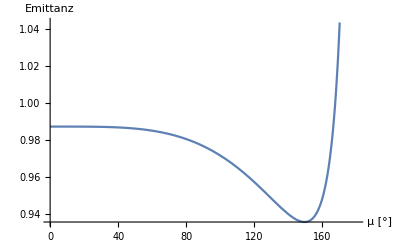

```mathematica
Plot[ϵ0//.minθ//.κphase//.γrel->10^6//.constants,{μ,0,180}, AxesLabel->{"μ [°]", "Emittanz"}]
```

Die Minimale Emittanz würde bei einem Phasenvorschub von 150° erreicht werden.

## Plot der Chromatizität

```mathematica
ξ:=-1/(Pi*√(2*κ^2-1))
```

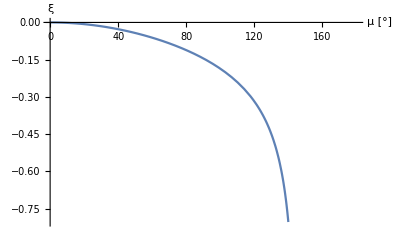

```mathematica
Plot[ξ//.κphase,{μ,0,180}, AxesLabel->{"μ [°]", "ξ"}]
```

Bei einem Phasenvorschub von 150 ° divergiert die Chormatizität, weshalb dies kein möglicher Arbeitspunkt ist.

## Zahlenbeispiele

```mathematica
lepParams = {μ-> 90 Degree, θ->-0.011, γrel -> 100000/0.511}
```

{μ→90 °,θ→-0.011,γrel→195695.}

```mathematica
ϵ0 //. κphase //.lepParams //.constants
```

1.70382